```mathematica
rts = {29.335705, 15.440684, 15.139352, 11.419552, 12.630046,8.446219, 9.047728, 7.975588, 9.227917, 7.669908, 8.679145, 11.277401, 9.084399, 10.462130, 8.270906, 8.509908};
rts = rts⟦1⟧ / rts;
```

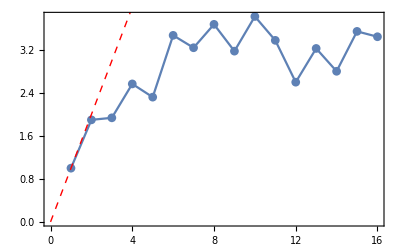

```mathematica
Show[
ListPlot[rts, Joined->True, PlotMarkers->Automatic, Frame->True, FrameStyle->Thick, ImageSize->400],
Plot[x, {x, 0, 8}, PlotStyle->{Thick, Red, Dashed}]
]
```